```mathematica
f1[x_]:=2*ArcTan[x]-x
```

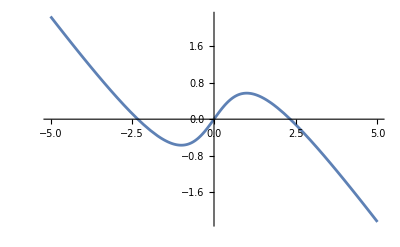

```mathematica
Plot[f1[x],{x,-5,5}]
```

```mathematica
Limit[f1[x],x->Infinity]
```

-∞

```mathematica
Limit[f1[x],x->-Infinity]
```

∞

```mathematica
f1'[x]
```

-1+2/(1+x^2)

```mathematica
Solve[f1'[x]==0,x]
```

{{x→-1},{x→1}}

```mathematica
Limit[f1[x]/x,x->Infinity]
```

-1

a = -1

```mathematica
Limit[f1[x]-(-1)*x,x->Infinity]
```

π

```mathematica
Limit[f1[x]/x,x->-Infinity]
```

-1

```mathematica
Limit[f1[x]-(-1)*x,x->-Infinity]
```

-π

```mathematica
Limit[f1[x]-((-1)*x+Pi),x->Infinity]
```

0

```mathematica
Limit[f1[x]-((-1)*(-Pi)),x->-Infinity]
```

∞

Ma asymptote ukośną lewostronną

```mathematica
FunctionDomain[f1[x],x]
```

True

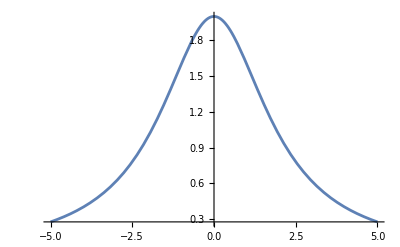

```mathematica
g[x_]:=8/(x^2+4)
Plot[g[x],{x,-5,5}]
```

```mathematica
P[x_]:=2*x*8/(x^2+4)
Plot[P[x],{x,-5,5}]
```

```mathematica
P'[x]
```

-(32 x^2)/((4+x^2)^2)+16/(4+x^2)

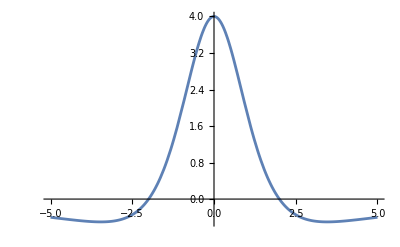

```mathematica
Plot[P'[x],{x,-5,5}]
```

```mathematica
P[2]
```

4

```mathematica
h[x_]:=Piecewise[{{2x,0<x<1/3},{1-x,1/3<x<1}}]
```

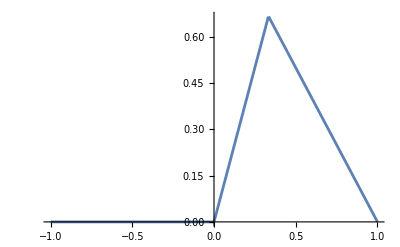

```mathematica
Plot[h[x],{x,-1,1}]
```

```mathematica
h2[x_]:=Piecewise[{{-1-x,-1<x<-1/3},{2x,-1/3<x<1/3},{1-x,1/3<x<1}}]
```

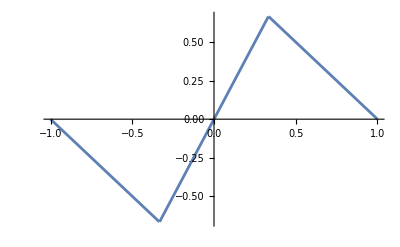

```mathematica
Plot[h2[x],{x,-1,1}]
```

```mathematica
ft2=FourierTrigSeries[h2[x],x,2,FourierParameters->{1,Pi}]
```

(3 √3 Sin[π x])/π^2+(3 √3 Sin[2 π x])/(4 π^2)

```mathematica
ft4=FourierTrigSeries[h2[x],x,4,FourierParameters->{1,Pi}]
```

(3 √3 Sin[π x])/π^2+(3 √3 Sin[2 π x])/(4 π^2)-(3 √3 Sin[4 π x])/(16 π^2)

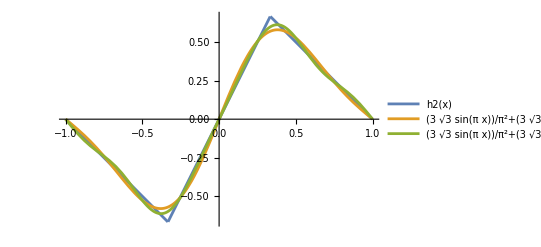

```mathematica
Plot[{h2[x],ft2,ft4},{x,-1,1},PlotLegends->"Expressions"]
```

```mathematica
f6[x_,y_]:=(x^2-x+y^2)/(x^2+y^4+3)
```

```mathematica
Plot3D[f6[x,y],{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=1]]
```

-Graphics3D-

```mathematica
Solve[D[f6[x,y],x]==0 &&D[f6[x,y],y]==0&&x^2+y^2<1,{x,y}]
```

{{x→-3+2 √3,y→0}}

```mathematica
D[f6[x,y],x]
```

-(2 x (-x+x^2+y^2))/((3+x^2+y^4)^2)+(-1+2 x)/(3+x^2+y^4)

```mathematica
D[f6[x,y],y]
```

-(4 y^3 (-x+x^2+y^2))/((3+x^2+y^4)^2)+(2 y)/(3+x^2+y^4)

```mathematica
D[f6[x,y],{{x,y},2}]//MatrixForm
```

((8 x^2 (-x+x^2+y^2))/((3+x^2+y^4)^3)-(4 x (-1+2 x))/((3+x^2+y^4)^2)-(2 (-x+x^2+y^2))/((3+x^2+y^4)^2)+2/(3+x^2+y^4) | (16 x y^3 (-x+x^2+y^2))/((3+x^2+y^4)^3)-(4 x y)/((3+x^2+y^4)^2)-(4 (-1+2 x) y^3)/((3+x^2+y^4)^2)
(16 x y^3 (-x+x^2+y^2))/((3+x^2+y^4)^3)-(4 x y)/((3+x^2+y^4)^2)-(4 (-1+2 x) y^3)/((3+x^2+y^4)^2) | (32 y^6 (-x+x^2+y^2))/((3+x^2+y^4)^3)-(16 y^4)/((3+x^2+y^4)^2)-(12 y^2 (-x+x^2+y^2))/((3+x^2+y^4)^2)+2/(3+x^2+y^4))

```mathematica
%/.{x->-3+2 √3,y->0}//MatrixForm
```

(-(4 (-3+2 √3) (-1+2 (-3+2 √3)))/((3+(-3+2 √3)^2)^2)+2/(3+(-3+2 √3)^2)+(8 (-3+2 √3)^2 (3-2 √3+(-3+2 √3)^2))/((3+(-3+2 √3)^2)^3)-(2 (3-2 √3+(-3+2 √3)^2))/((3+(-3+2 √3)^2)^2) | 0
0 | 2/(3+(-3+2 √3)^2))

```mathematica
Det[%]
```

16128/((3+(-3+2 √3)^2)^4)-(9312 √3)/((3+(-3+2 √3)^2)^4)-456/((3+(-3+2 √3)^2)^3)+(264 √3)/((3+(-3+2 √3)^2)^3)+4/((3+(-3+2 √3)^2)^2)

```mathematica
D[f6[x,y],{x,2}]/.{x->0,y->0}
```

2/3

```mathematica
f6[-3+2 √3,0]
```

(3-2 √3+(-3+2 √3)^2)/(3+(-3+2 √3)^2)